```mathematica
(*Reallocate Memory to store the data*)
Needs["JLink`"]
ReinstallJava[JVMArguments -> "-Xmx1024m"];
```

```mathematica
(*Set Working Directory*)
SetDirectory["/home/adam/Desktop/Modeling/Data"]
```

/home/adam/Desktop/Modeling/Data

```mathematica
(*Load the data*)
Datastuff= Import["ProblemC56Var.xlsx"];
```

```mathematica
Clear[f]
(*To turn years to Ints*)
f[{x_,y_,z_,a_}]:={x,y,IntegerPart[z],a}
```

```mathematica
Clear[ModifiedData]
ModifiedData=Map[f,Datastuff[[1]]];
```

```mathematica
Clear[AZData,TXData,NMData,CAData]
(*Separate Data by state*)
AZData=Cases[ModifiedData,{_,"AZ",_,_}];
TXData=Cases[ModifiedData,{_,"TX",_,_}];
NMData=Cases[ModifiedData,{_,"NM",_,_}];
CAData=Cases[ModifiedData,{_,"CA",_,_}];
StateData={AZData,TXData,NMData,CAData};
Produced=Drop[Map[First,Datastuff[[2]]],2];
Consumed=Flatten@Drop[Drop[Map[Take[#,{4}]&,Datastuff[[2]]],2],-34];
```

```mathematica
Clear[TimeFunc,VarFunc,RemoveState,ProducedVars,ConsumedVars,DataFunc]
VarFunc[{a_,b_,c_,d_}]:={a}
TimeFunc[{a_,b_,c_,d_}]:={c,d}
RemoveState[{a_,b_,c_,d_}]:={a,c,d}
DataFunc[{a_,b_,c_,d_}]:=d
ProducedVars[dataset_]:=Map[Cases[dataset,#]&,Table[{i,_,_,_},{i,Produced}]];
ConsumedVars[dataset_]:=Map[Cases[dataset,#]&,Table[{i,_,_,_},{i,Consumed}]];
```

```mathematica
Clear[AZProduced,TXProduced,NMProduced,CAProduced]
{AZProduced,TXProduced,NMProduced,CAProduced}=Map[ProducedVars,StateData];
```

```mathematica
Clear[AZConsumed,TXConsumed,NMConsumed,CAConsumed]
{AZConsumed,TXConsumed,NMConsumed,CAConsumed}=Map[ConsumedVars,StateData];
```

```mathematica
Clear[TimeRemove]
TimeRemove[dataset_]:=Map[TimeFunc[#]&,dataset]
```

```mathematica
Clear[CalculatingROC,OverlappedLists,Pairs,CROC];
CalculatingROC[{a_,b_}]:=b-a;
CROC[data_]:=Table[CalculatingROC[i],{i,data}];
OverlappedLists[data_]:=Map[Partition[#,2,1]&,data];
Pairs[data_]:=Map[Partition[#,2,1]&,data];
```

```mathematica
{AZPart,TXPart,NMPart,CAPart}=Table[Map[DataFunc,i,{2}],{i,{AZProduced,TXProduced,NMProduced,CAProduced}}];
```

```mathematica
Clear[LastModelV2];
LastModelV2[data_]:=Module[{d=data},
{PyramidalSubtractionAZ,PyramidalSubtractionTX,PyramidalSubtractionNM,PyramidalSubtractionCA}=Map[OverlappedLists,d];
{PyramidalSubtractionAZ,PyramidalSubtractionTX,PyramidalSubtractionNM,PyramidalSubtractionCA}=Map[Table[CROC[i],{i,#}]&,{PyramidalSubtractionAZ,PyramidalSubtractionTX,PyramidalSubtractionNM,PyramidalSubtractionCA}];
lists=Append[lists,Table[Map[Last,i],{i,{PyramidalSubtractionAZ,PyramidalSubtractionTX,PyramidalSubtractionNM,PyramidalSubtractionCA}}]];
];
```

```mathematica
Clear[ModelV2];
ModelV2[dataset_]:=Module[
{data0=dataset},
Clear[AZPart,TXPart,NMPart,CAPart];
{AZPart,TXPart,NMPart,CAPart}=Table[Map[DataFunc,i,{2}],{i,data0}];

LastModelV2[{PyramidalSubtractionAZ,PyramidalSubtractionTX,PyramidalSubtractionNM,PyramidalSubtractionCA}];
Clear[n,lists,PyramidalSubtractionAZ,PyramidalSubtractionTX,PyramidalSubtractionNM,PyramidalSubtractionCA];
n=0;
Print[ProgressIndicator[Dynamic[n],{0,49}]];
lists={};
lists=Append[lists,Table[Map[Last,i],{i,{AZPart,TXPart,NMPart,CAPart}}]];
LastModelV2[{AZPart,TXPart,NMPart,CAPart}];
While[
n<49,
{LastModelV2[{PyramidalSubtractionAZ,PyramidalSubtractionTX,PyramidalSubtractionNM,PyramidalSubtractionCA}]}
;n++];
Clear[TaylorSeriesLastV2];
TaylorSeriesLastV2[x_,{n0_}]:=x*(t-49)^(n0-1)*(1/Factorial[n0]);
Clear[AZSlopes,TXSlopes,NMSlopes,CASlopes];
AZSlopes=Transpose[PadRight[Map[Part[#,1]&,Table[Map[DeleteCases[#,_Last]&,i],{i,Drop[lists,-1]}]]]];
TXSlopes=Transpose[PadRight[Map[Part[#,2]&,Table[Map[DeleteCases[#,_Last]&,i],{i,Drop[lists,-1]}]]]];
NMSlopes=Transpose[PadRight[Map[Part[#,3]&,Table[Map[DeleteCases[#,_Last]&,i],{i,Drop[lists,-1]}]]]];
CASlopes=Transpose[PadRight[Map[Part[#,4]&,Table[Map[DeleteCases[#,_Last]&,i],{i,Drop[lists,-1]}]]]];
AZMonomials=Table[MapIndexed[TaylorSeriesLastV2,i],{i,AZSlopes}];
TXMonomials=Table[MapIndexed[TaylorSeriesLastV2,i],{i,TXSlopes}];
NMMonomials=Table[MapIndexed[TaylorSeriesLastV2,i],{i,NMSlopes}];
CAMonomials=Table[MapIndexed[TaylorSeriesLastV2,i],{i,CASlopes}];
AZSystemConsumption=Map[Total,AZMonomials];
TXSystemConsumption=Map[Total,TXMonomials];
NMSystemConsumption=Map[Total,NMMonomials];
CASystemConsumption=Map[Total,CAMonomials];
Return[{AZSystemConsumption,TXSystemConsumption,NMSystemConsumption,CASystemConsumption}];
]
```

```mathematica
(*DO NOT REMOVE*)
LastModelV2[{AZProduced,TXProduced,NMProduced,CAProduced}];
```

Append::normal: Nonatomic expression expected at position 1 in Append[lists,{{{0,0,1,-55.2095},{0,0,1,-9.28478},«42»,{0,0,1,-2.85497}},«2»,{{0,0,1,-«18»},«43»,{«1»}}}].

$RecursionLimit::reclim2: Recursion depth of 1024 exceeded during evaluation of Append[lists,{{{0,0,1,-55.2095},{0,0,1,-9.28478},«42»,{0,0,1,-2.85497}},«2»,{{0,0,1,-«18»},«43»,{«1»}}}].

```mathematica
LastsSystem=ModelV2[{AZProduced,TXProduced,NMProduced,CAProduced}];
```

Last::nolast: {} has zero length and no last element.

General::stop: Further output of Last::nolast will be suppressed during this calculation.

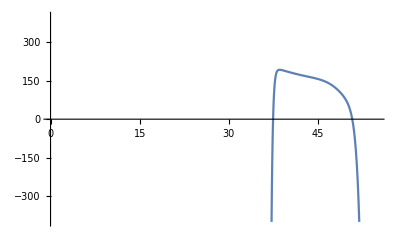

```mathematica
Plot[LastsSystem[[1]][[1]],{t,30,55},PlotRange->{{0,55},{-400,400}}]
```

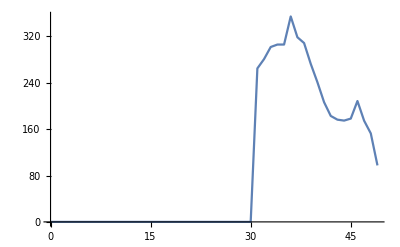

```mathematica
Clear[LastModel];
LastModel[data_]:=Module[{d=data},
{PyramidalSubtractionAZ,PyramidalSubtractionTX,PyramidalSubtractionNM,PyramidalSubtractionCA}=Map[OverlappedLists,d];
{PyramidalSubtractionAZ,PyramidalSubtractionTX,PyramidalSubtractionNM,PyramidalSubtractionCA}=Map[Table[CROC[i],{i,#}]&,{PyramidalSubtractionAZ,PyramidalSubtractionTX,PyramidalSubtractionNM,PyramidalSubtractionCA}];
lists=Append[lists,Table[Map[Median,i],{i,{PyramidalSubtractionAZ,PyramidalSubtractionTX,PyramidalSubtractionNM,PyramidalSubtractionCA}}]];
];
```

```mathematica
Clear[Model];
Model[dataset_]:=Module[
{data0=dataset},
Clear[AZPart,TXPart,NMPart,CAPart];
{AZPart,TXPart,NMPart,CAPart}=Table[Map[DataFunc,i,{2}],{i,data0}];
{AZPart,TXPart,NMPart,CAPart}=Table[Map[DeleteDuplicates[Chop[#]]&,i],{i,{AZPart,TXPart,NMPart,CAPart}}];

Clear[CalculatingROC,OverlappedLists,Pairs,CROC];
CalculatingROC[{a_,b_}]:=b-a;
CROC[data_]:=Table[CalculatingROC[i],{i,data}];
OverlappedLists[data_]:=Map[Partition[#,2,1]&,data];
Pairs[data_]:=Map[Partition[#,2,1]&,data];

LastModel[{PyramidalSubtractionAZ,PyramidalSubtractionTX,PyramidalSubtractionNM,PyramidalSubtractionCA}];
Clear[n,lists,PyramidalSubtractionAZ,PyramidalSubtractionTX,PyramidalSubtractionNM,PyramidalSubtractionCA];
n=0;
Print[ProgressIndicator[Dynamic[n],{0,49}]];
lists={};
lists=Append[lists,Table[Map[Median,i],{i,{AZPart,TXPart,NMPart,CAPart}}]];
LastModel[{AZPart,TXPart,NMPart,CAPart}];
While[
n<49,
{LastModel[{PyramidalSubtractionAZ,PyramidalSubtractionTX,PyramidalSubtractionNM,PyramidalSubtractionCA}]}
;n++];
Clear[TaylorSeriesLast];
TaylorSeriesLast[x_,{n0_}]:=x*(t-30)^(n0-1)*(1/Factorial[n0]);
Clear[AZSlopes,TXSlopes,NMSlopes,CASlopes];

AZSlopes=Transpose[PadRight[Map[Part[#,1]&,Table[Map[DeleteCases[#,_Median]&,i],{i,Drop[lists,-1]}]]]];

TXSlopes=Transpose[PadRight[Map[Part[#,2]&,Table[Map[DeleteCases[#,_Median]&,i],{i,Drop[lists,-1]}]]]];

NMSlopes=Transpose[PadRight[Map[Part[#,3]&,Table[Map[DeleteCases[#,_Median]&,i],{i,Drop[lists,-1]}]]]];

CASlopes=Transpose[PadRight[Map[Part[#,4]&,Table[Map[DeleteCases[#,_Median]&,i],{i,Drop[lists,-1]}]]]];

AZMonomials=Table[MapIndexed[TaylorSeriesLast,i],{i,AZSlopes}];

TXMonomials=Table[MapIndexed[TaylorSeriesLast,i],{i,TXSlopes}];

NMMonomials=Table[MapIndexed[TaylorSeriesLast,i],{i,NMSlopes}];

CAMonomials=Table[MapIndexed[TaylorSeriesLast,i],{i,CASlopes}];

AZSystemConsumption=Map[Total,AZMonomials];

TXSystemConsumption=Map[Total,TXMonomials];

NMSystemConsumption=Map[Total,NMMonomials];

CASystemConsumption=Map[Total,CAMonomials];

Return[{AZSystemConsumption,TXSystemConsumption,NMSystemConsumption,CASystemConsumption}];
]
```

```mathematica
LastModel[{AZPart,TXPart,NMPart,CAPart}]
```

```mathematica
MedianSystem=Model[{AZProduced,TXProduced,NMProduced,CAProduced}];
```

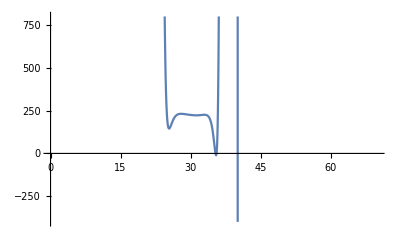

```mathematica
Plot[MedianSystem[[1]][[1]],{t,0,70},PlotRange->{{0,70},{-400,800}}]
```

```mathematica
Clear[LastModelFirst];
LastModelFirst[data_]:=Module[{d=data},
{PyramidalSubtractionAZ,PyramidalSubtractionTX,PyramidalSubtractionNM,PyramidalSubtractionCA}=Map[OverlappedLists,d];
{PyramidalSubtractionAZ,PyramidalSubtractionTX,PyramidalSubtractionNM,PyramidalSubtractionCA}=Map[Table[CROC[i],{i,#}]&,{PyramidalSubtractionAZ,PyramidalSubtractionTX,PyramidalSubtractionNM,PyramidalSubtractionCA}];
lists=Append[listsFirst,Table[Map[First,i],{i,{PyramidalSubtractionAZ,PyramidalSubtractionTX,PyramidalSubtractionNM,PyramidalSubtractionCA}}]];
];
```

```mathematica
Clear[ModelFirst];
ModelFirst[dataset_]:=Module[
{data0=dataset},
Clear[AZPart,TXPart,NMPart,CAPart];
{AZPart,TXPart,NMPart,CAPart}=Table[Map[DataFunc,i,{2}],{i,data0}];
{AZPart,TXPart,NMPart,CAPart}=Table[Map[DeleteDuplicates[Chop[#]]&,i],{i,{AZPart,TXPart,NMPart,CAPart}}];

Clear[CalculatingROC,OverlappedLists,Pairs,CROC];
CalculatingROC[{a_,b_}]:=b-a;
CROC[data_]:=Table[CalculatingROC[i],{i,data}];
OverlappedLists[data_]:=Map[Partition[#,2,1]&,data];
Pairs[data_]:=Map[Partition[#,2,1]&,data];

LastModelFirst[{PyramidalSubtractionAZ,PyramidalSubtractionTX,PyramidalSubtractionNM,PyramidalSubtractionCA}];
Clear[n,listsFirst,PyramidalSubtractionAZ,PyramidalSubtractionTX,PyramidalSubtractionNM,PyramidalSubtractionCA];
n=0;
Print[ProgressIndicator[Dynamic[n],{0,49}]];
listsFirst={};
listsFirst=Append[listsFirst,Table[Map[First,i],{i,{AZPart,TXPart,NMPart,CAPart}}]];
LastModelFirst[{AZPart,TXPart,NMPart,CAPart}];
While[
n<49,
{LastModelFirst[{PyramidalSubtractionAZ,PyramidalSubtractionTX,PyramidalSubtractionNM,PyramidalSubtractionCA}],
listsFirst=Append[listsFirst,Table[Map[First,i],{i,{PyramidalSubtractionAZ,PyramidalSubtractionTX,PyramidalSubtractionNM,PyramidalSubtractionCA}}]]}
;n++];
(*Return[listsFirst];*)
Clear[TaylorSeriesFirst];
TaylorSeriesFirst[x_,{n0_}]:=x*(t-20)^(n0-1)*(1/Factorial[n0]);
Clear[AZSlopesFirst,TXSlopesFirst,NMSlopesFirst,CASlopesFirst];
AZSlopesFirst=Transpose[PadRight[Map[Part[#,1]&,Table[Map[DeleteCases[#,_First]&,i],{i,Drop[listsFirst,-1]}]]]];
TXSlopesFirst=Transpose[PadRight[Map[Part[#,2]&,Table[Map[DeleteCases[#,_First]&,i],{i,Drop[listsFirst,-1]}]]]];
NMSlopesFirst=Transpose[PadRight[Map[Part[#,3]&,Table[Map[DeleteCases[#,_First]&,i],{i,Drop[listsFirst,-1]}]]]];
CASlopesFirst=Transpose[PadRight[Map[Part[#,4]&,Table[Map[DeleteCases[#,_First]&,i],{i,Drop[listsFirst,-1]}]]]];
AZMonomialsFirst=Table[MapIndexed[TaylorSeriesFirst,i],{i,AZSlopesFirst}];
TXMonomialsFirst=Table[MapIndexed[TaylorSeriesFirst,i],{i,TXSlopesFirst}];
NMMonomialsFirst=Table[MapIndexed[TaylorSeriesFirst,i],{i,NMSlopesFirst}];
CAMonomialsFirst=Table[MapIndexed[TaylorSeriesFirst,i],{i,CASlopesFirst}];
AZSystemConsumption=Map[Total,AZMonomialsFirst];
TXSystemConsumption=Map[Total,TXMonomialsFirst];
NMSystemConsumption=Map[Total,NMMonomialsFirst];
CASystemConsumption=Map[Total,CAMonomialsFirst];
Return[{AZSystemConsumption,TXSystemConsumption,NMSystemConsumption,CASystemConsumption}];
]
```

```mathematica
FirstsSystem=ModelFirst[{AZProduced,TXProduced,NMProduced,CAProduced}];
```

First::nofirst: {} has zero length and no first element.

General::stop: Further output of First::nofirst will be suppressed during this calculation.

Append::normal: Nonatomic expression expected at position 1 in Append[listsFirst,{{First[{}],First[{}],First[{}],First[{}],«37»,First[{}],First[{}],First[{}],First[{}]},«2»,{First[{}],«44»}}].

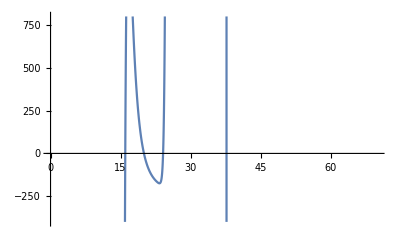

```mathematica
Plot[FirstsSystem[[1]][[1]],{t,0,70},PlotRange->{{0,70},{-400,800}}]
```